```mathematica
M=1;
Λ=1;
g=1.1;
f[x_]=1/Λ*(g(SphericalBesselJ[0,x])^2)/(1+g*x*SphericalBesselJ[0,x]*SphericalBesselY[0,x]-I*g*x*(SphericalBesselJ[0,x])^2);
cotd[x_]=1/(f[x]*x)+I;
del[x_]=ArcCot[cotd[x]];
scatlen =-del[0.0001]/0.0001
```

11.+0. ⅈ

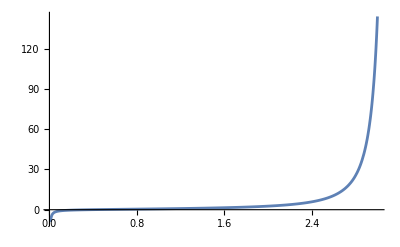

```mathematica
Plot[{cotd[x]},{x,0.01,3},PlotRange->All]
```

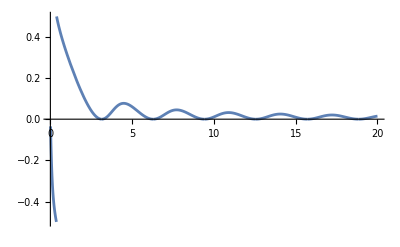

```mathematica
Plot[{del[x]/Pi},{x,0.01,20},PlotRange->All]
```

```mathematica
root1=Re[z/.FindRoot[{cotd[z]==0},{z,0.1}]]
```

0.374493

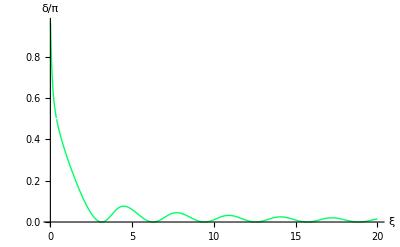

```mathematica
delta=Plot[Piecewise[{{1+del[z]/Pi,z<root1}},del[z]/Pi],{z,0.01,20},PlotRange->All,AxesLabel->{"ξ","δ/π"},PlotStyle->{Hue[0.4],Thick},LabelStyle->Medium]
```

```mathematica
ComplexPlot3D[f[x],{x,-5-3I,5+3I}]
```

-Graphics3D-

```mathematica
NSolve[1/f[z]==0,z]
```

NSolve::fexp: Warning: NSolve used FunctionExpand to transform the system. Since FunctionExpand transformation rules are only generically correct, the solution set might have been altered.

{{z→0.-0.103573 ⅈ},{z→-3.73041-1.0972 ⅈ},{z→-6.93934-1.38475 ⅈ},{z→-10.1118-1.56585 ⅈ},{z→-13.2715-1.69853 ⅈ},{z→-16.4252-1.80332 ⅈ},{z→-19.5755-1.88994 ⅈ},{z→-22.7236-1.96376 ⅈ},{z→-25.8704-2.02809 ⅈ},{z→-29.0162-2.08508 ⅈ},{z→-32.1612-2.13625 ⅈ},{z→-35.3057-2.18266 ⅈ},{z→-38.4498-2.22514 ⅈ},{z→-41.5935-2.26429 ⅈ},{z→-44.737-2.3006 ⅈ},{z→-47.8802-2.33445 ⅈ}}